```mathematica
hhh=({{-2, 1/2, 1/2, 0, 0, 0, 0, 0, 0, 0}, {1/2, -1, 1/2, 0, 0, 0, 0, 0, 0, 0}, {1/2, 1/2, -2, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 1, -2, 1/2, 1/2, 0, 0, 0, 0}, {0, 0, 0, 1/2, -1, 1/2, 0, 0, 0, 0}, {0, 0, 0, 1/2, 1/2, -2, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, -1, -1, 0, 0}, {0, 0, 0, 0, 0, 0, -1, -2, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, -1, -1}, {0, 0, 0, 0, 0, 0, 0, 0, -1, -2}})
```

SparseArray[<30>,{10,10}]

```mathematica
MatrixForm[hhh]
```

(-2 | 1/2 | 1/2 | 0 | 0 | ⅇ^(-ⅈ kx) | 0 | 0 | 0 | 0
1/2 | -1 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/2 | 1/2 | -2 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | -2 | 1/2 | 1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/2 | -1 | 1/2 | 0 | 0 | 0 | 0
ⅇ^(ⅈ kx) | 0 | 0 | 1/2 | 1/2 | -2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | -2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -2)

```mathematica
hh=Table[0,{i,10},{j,10}];
MatrixForm[hh]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
For[i=1,i≤10,i++,For[j=1,j≤10,j++,hh[[i]][[j]]=hhh[[i]][[j]]]];
```

```mathematica
MatrixForm[hh]
```

```mathematica
hh=({{-2, 1/2, 1/2, 0, 0, 0, 0, 0, 0, 0}, {1/2, -1, 1/2, 0, 0, 0, 0, 0, 0, 0}, {1/2, 1/2, -2, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 1, -2, 1/2, 1/2, 0, 0, 0, 0}, {0, 0, 0, 1/2, -1, 1/2, 0, 0, 0, 0}, {0, 0, 0, 1/2, 1/2, -2, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, -1, -1, 0, 0}, {0, 0, 0, 0, 0, 0, -1, -2, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, -1, -1}, {0, 0, 0, 0, 0, 0, 0, 0, -1, -2}})
```

{{-2,1/2,1/2,0,0,0,0,0,0,0},{1/2,-1,1/2,0,0,0,0,0,0,0},{1/2,1/2,-2,1,0,0,0,0,0,0},{0,0,1,-2,1/2,1/2,0,0,0,0},{0,0,0,1/2,-1,1/2,0,0,0,0},{0,0,0,1/2,1/2,-2,0,0,0,0},{0,0,0,0,0,0,-1,-1,0,0},{0,0,0,0,0,0,-1,-2,0,0},{0,0,0,0,0,0,0,0,-1,-1},{0,0,0,0,0,0,0,0,-1,-2}}

```mathematica
Eigensystem[hh+0.0]
```

{{-3.24464,-2.61803,-2.61803,-2.28078,-2.14458,-1.5,-0.610771,-0.381966,-0.381966,-0.219224},{{-0.227204,-0.0969746,0.662551,-0.662551,0.0969746,0.227204,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.525731,0.850651,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.525731,0.850651},{0.657192,-0.184524,-0.184524,-0.184524,-0.184524,0.657192,0.,0.,0.,0.},{0.603509,-0.332767,0.158251,-0.158251,0.332767,-0.603509,0.,0.,0.,0.},{2.77556×10^-16,0.5,-0.5,-0.5,0.5,-4.87814×10^-16,0.,0.,0.,0.},{-0.290096,-0.616329,-0.18969,0.18969,0.616329,0.290096,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.850651,-0.525731,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.850651,-0.525731},{-0.260956,-0.464705,-0.464705,-0.464705,-0.464705,-0.260956,0.,0.,0.,0.}}}

```mathematica
MatrixForm[DiagonalMatrix[{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}]]
```

```mathematica
HH[a_,b_]:=({{1, 0, 0, a, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {a, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, a, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, a, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, a, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, a, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0, 0, a, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, a, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, a, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, a, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, a, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, a, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, a}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, a, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, a, 1}})+(b-1)DiagonalMatrix[{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}]
```

```mathematica
Eigenvalues[HH[1.0,2]]
```

{3.,2.92388+0.382683 ⅈ,2.92388-0.382683 ⅈ,2.70711+0.707107 ⅈ,2.70711-0.707107 ⅈ,2.38268+0.92388 ⅈ,2.38268-0.92388 ⅈ,2.+1. ⅈ,2.-1. ⅈ,1.61732+0.92388 ⅈ,1.61732-0.92388 ⅈ,1.29289+0.707107 ⅈ,1.29289-0.707107 ⅈ,1.07612+0.382683 ⅈ,1.07612-0.382683 ⅈ,1.}

```mathematica
MatrixForm[HH[2,1]]
```

(1 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 1)

```mathematica
GG[a_,b_]:=Transpose[HH[a,b]]
```

```mathematica
Eigensystem[GG[1,1.0].HH[1,1.0]]
```

{{3.96386,3.85674,3.68251,3.44747,3.16011,2.83083,2.47152,2.09516,1.71537,1.34586,1.,0.690279,0.427894,0.222329,0.0810141,0.00905615},{{-0.0980867,-0.0330943,-0.215215,-0.159534,-0.301511,-0.263118,-0.344612,-0.329007,-0.338341,-0.347761,-0.283599,-0.316693,-0.188227,-0.240255,-0.0658888,-0.129396},{-0.188227,-0.0658888,-0.338341,-0.283599,-0.301511,-0.344612,-0.0980867,-0.215215,0.159534,0.0330943,0.329007,0.263118,0.316693,0.347761,0.129396,0.240255},{-0.263118,-0.0980867,-0.316693,-0.344612,8.8124×10^-16,-0.188227,0.316693,0.188227,0.263118,0.344612,-0.0980867,0.0980867,-0.344612,-0.263118,-0.188227,-0.316693},{-0.316693,-0.129396,-0.159534,-0.329007,0.301511,0.0980867,0.188227,0.338341,-0.283599,-0.0658888,-0.215215,-0.344612,0.263118,0.0330943,0.240255,0.347761},{-0.344612,-0.159534,0.0658888,-0.240255,0.301511,0.316693,-0.263118,0.0330943,-0.129396,-0.338341,0.347761,0.188227,-0.0980867,0.215215,-0.283599,-0.329007},{0.344612,0.188227,-0.263118,0.0980867,-7.77156×10^-16,-0.316693,0.263118,0.316693,-0.344612,-0.0980867,0.188227,-0.188227,0.0980867,0.344612,-0.316693,-0.263118},{-0.316693,-0.215215,0.347761,0.0658888,-0.301511,0.0980867,0.188227,-0.240255,-0.0330943,0.329007,-0.129396,-0.344612,0.263118,0.283599,-0.338341,-0.159534},{0.263118,0.240255,-0.283599,-0.215215,0.301511,0.188227,-0.316693,-0.159534,0.329007,0.129396,-0.338341,-0.0980867,0.344612,0.0658888,-0.347761,-0.0330943},{0.188227,0.263118,-0.0980867,-0.316693,7.77156×10^-16,0.344612,0.0980867,-0.344612,-0.188227,0.316693,0.263118,-0.263118,-0.316693,0.188227,0.344612,-0.0980867},{0.0980867,0.283599,0.129396,-0.347761,-0.301511,0.263118,0.344612,-0.0658888,-0.240255,-0.159534,0.0330943,0.316693,0.188227,-0.338341,-0.329007,0.215215},{-1.19349×10^-15,0.301511,0.301511,-0.301511,-0.301511,7.46003×10^-16,-7.49401×10^-16,0.301511,0.301511,-0.301511,-0.301511,-1.25529×10^-15,-3.46945×10^-15,0.301511,0.301511,-0.301511},{-0.0980867,0.316693,0.344612,-0.188227,-1.249×10^-16,-0.263118,-0.344612,0.263118,0.0980867,0.188227,0.316693,-0.316693,-0.188227,-0.0980867,-0.263118,0.344612},{0.188227,-0.329007,-0.240255,0.0330943,-0.301511,0.344612,0.0980867,0.129396,0.347761,-0.283599,0.0658888,-0.263118,-0.316693,0.159534,-0.215215,0.338341},{-0.263118,0.338341,0.0330943,0.129396,0.301511,-0.188227,0.316693,-0.347761,0.0658888,-0.215215,-0.240255,0.0980867,-0.344612,0.329007,-0.159534,0.283599},{0.316693,-0.344612,0.188227,-0.263118,-7.74034×10^-15,-0.0980867,-0.188227,0.0980867,-0.316693,0.263118,-0.344612,0.344612,-0.263118,0.316693,-0.0980867,0.188227},{-0.344612,0.347761,-0.329007,0.338341,-0.301511,0.316693,-0.263118,0.283599,-0.215215,0.240255,-0.159534,0.188227,-0.0980867,0.129396,-0.0330943,0.0658888}}}

```mathematica
MatrixForm[GG[a,b].HH[a,b]]
```

```mathematica
LL[a_,b_]:=({{(a^2+b^2)/2, a b, 0, a b, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {a b, (a^2+b^2)/2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, a^2+b^2, a b, 0, a b, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {a b, 0, a b, a^2+b^2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, a^2+b^2, a b, 0, a b, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, a b, 0, a b, a^2+b^2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, a^2+b^2, a b, 0, a b, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, a b, 0, a b, a^2+b^2, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, a^2+b^2, a b, 0, a b, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, a b, 0, a b, a^2+b^2, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, a^2+b^2, a b, 0, a b, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, a b, 0, a b, a^2+b^2, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, a^2+b^2, a b, 0, a b}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, a b, 0, a b, a^2+b^2, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, (a^2+b^2)/2, a b}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, a b, 0, a b, (a^2+b^2)/2}})
```

```mathematica
MatrixForm[GG[b,a].HH[b,a]]
```

(a^2+b^2 | a b | 0 | a b | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
a b | a^2+b^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a b | 0
0 | 0 | a^2+b^2 | a b | 0 | a b | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
a b | 0 | a b | a^2+b^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | a^2+b^2 | a b | 0 | a b | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | a b | 0 | a b | a^2+b^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | a^2+b^2 | a b | 0 | a b | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | a b | 0 | a b | a^2+b^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a^2+b^2 | a b | 0 | a b | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | a b | 0 | a b | a^2+b^2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a^2+b^2 | a b | 0 | a b | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a b | 0 | a b | a^2+b^2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a^2+b^2 | a b | 0 | a b
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a b | 0 | a b | a^2+b^2 | 0 | 0
0 | a b | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a^2+b^2 | a b
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a b | 0 | a b | a^2+b^2)

```mathematica
({{a^2+b^2, a b, 0, a b, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {a b, a^2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, a^2+b^2, a b, 0, a b, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {a b, 0, a b, a^2+b^2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, a^2+b^2, a b, 0, a b, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, a b, 0, a b, a^2+b^2, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, a^2+b^2, a b, 0, a b, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, a b, 0, a b, a^2+b^2, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, a^2+b^2, a b, 0, a b, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, a b, 0, a b, a^2+b^2, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, a^2+b^2, a b, 0, a b, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, a b, 0, a b, a^2+b^2, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, a^2+b^2, a b, 0, a b}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, a b, 0, a b, a^2+b^2, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, a^2+b^2, a b}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, a b, 0, a b, a^2+b^2}})
```

{{a^2+b^2,a b,0,a b,0,0,0,0,0,0,0,0,0,0,0,0},{a b,a^2,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,a^2+b^2,a b,0,a b,0,0,0,0,0,0,0,0,0,0},{a b,0,a b,a^2+b^2,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,a^2+b^2,a b,0,a b,0,0,0,0,0,0,0,0},{0,0,a b,0,a b,a^2+b^2,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,a^2+b^2,a b,0,a b,0,0,0,0,0,0},{0,0,0,0,a b,0,a b,a^2+b^2,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,a^2+b^2,a b,0,a b,0,0,0,0},{0,0,0,0,0,0,a b,0,a b,a^2+b^2,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,a^2+b^2,a b,0,a b,0,0},{0,0,0,0,0,0,0,0,a b,0,a b,a^2+b^2,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,a^2+b^2,a b,0,a b},{0,0,0,0,0,0,0,0,0,0,a b,0,a b,a^2+b^2,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,a^2+b^2,a b},{0,0,0,0,0,0,0,0,0,0,0,0,a b,0,a b,a^2+b^2}}

```mathematica
KK[a_,b_]:=GG[a,b].HH[a,b]
```

```mathematica
Eigenvalues[KK[2,1.0]]
```

```mathematica
Eigenvalues[GG[2,1.0]]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

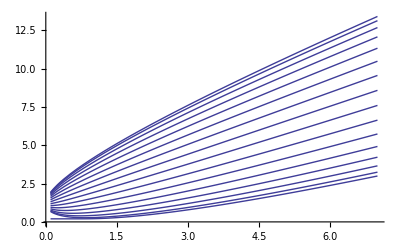

```mathematica
Plot[Eigenvalues[KK[1,Sqrt[X]]]+0.2,{X,0.1,7}]
```

```mathematica
Eigenvalues[LL[2,1.0]]
```

{8.90017,8.60615,8.13419,7.51112,6.77444,5.97378,5.17534,4.45984,3.86275,3.3006,2.68683,2.06086,1.51733,1.13902,-0.0513567,-0.0510437}

```mathematica
MatrixForm[KroneckerProduct[IdentityMatrix[8],I PauliMatrix[2]]]
```

```mathematica
AA=({{0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {-1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, -1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, -1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, -1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, -1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -1, 0}})
```

{{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0}}

```mathematica
Eigenvalues[-ZI AA.(GG[2,1.0].HH[2,1])]
```

{-6.51043-1.0842×10^-16 ⅈ,6.51043+7.88327×10^-16 ⅈ,-5.95651-5.83539×10^-16 ⅈ,5.95651+6.5196×10^-16 ⅈ,5.15705-1.38096×10^-16 ⅈ,-5.15705+1.04053×10^-15 ⅈ,-4.26775-4.21858×10^-16 ⅈ,4.26775-6.17031×10^-17 ⅈ,-3.44342-8.2812×10^-16 ⅈ,3.44342+6.06448×10^-16 ⅈ,2.79398+2.22437×10^-16 ⅈ,-2.79398+1.99966×10^-15 ⅈ,2.37952+4.41992×10^-16 ⅈ,-2.37952-7.47384×10^-16 ⅈ,0.0000511796+2.83884×10^-11 ⅈ,-0.0000511796-2.83878×10^-11 ⅈ}

```mathematica
MatrixForm[IdentityMatrix[2]]
```

```mathematica
LLL=({{AAA, BBB Exp[I k]}, {CCC, DDD}})
```

```mathematica
{{AAA,BBB ⅇ^(ⅈ k)},{CCC,DDD}}
Eigenvalues[LLL]
```

{{AAA,BBB ⅇ^(ⅈ k)},{CCC,DDD}}

{1/2 (AAA+DDD-√(AAA^2-2 AAA DDD+DDD^2+4 BBB CCC ⅇ^(ⅈ k))),1/2 (AAA+DDD+√(AAA^2-2 AAA DDD+DDD^2+4 BBB CCC ⅇ^(ⅈ k)))}

```mathematica
Eigenvalues[]
```

```mathematica
Eigensystem[GG[2.0,1].HH[2.0,1]]
```

{{8.92623,8.7076,8.35203,7.87239,7.28607,6.61434,5.88158,5.11444,4.34091,3.58936,2.88766,2.26243,1.73859,1.33943,1.08693,5.2388×10^-10},{{-0.088737,-0.0223907,-0.209284,-0.15181,-0.299239,-0.259039,-0.345454,-0.328403,-0.341171,-0.349763,-0.287018,-0.319996,-0.19091,-0.243454,-0.0668963,-0.131325},{-0.171545,-0.0445133,-0.335465,-0.273498,-0.310376,-0.348387,-0.110414,-0.226988,0.151757,0.022302,0.328425,0.259026,0.320051,0.349809,0.131353,0.243502},{0.24297,0.0660961,0.32876,0.341125,0.0230032,0.209881,-0.31015,-0.171327,-0.273921,-0.348488,0.0885427,-0.110606,0.345553,0.259005,0.191017,0.320147},{0.298465,0.0868592,0.192418,0.341794,-0.286409,-0.0654445,-0.210363,-0.345895,0.273229,0.0437729,0.227482,0.348637,-0.258977,-0.0219295,-0.243707,-0.350011},{0.334756,0.106507,-0.0191285,0.276131,-0.321491,-0.297995,0.242072,-0.0694801,0.153621,0.346178,-0.348604,-0.170583,0.0881251,-0.227883,0.287492,0.328613},{-0.350104,-0.124718,0.222672,-0.157876,0.0498366,0.33761,-0.289875,-0.297383,0.341053,0.0634045,-0.170027,0.211883,-0.111775,-0.349125,0.320754,0.258903},{0.34445,0.141122,-0.33973,0.0107077,0.269002,-0.160457,-0.146008,0.279031,-0.00535449,-0.34339,0.155677,0.34103,-0.275752,-0.272409,0.34225,0.15086},{0.319427,0.155271,-0.327266,-0.136993,0.334033,0.118267,-0.339707,-0.0991533,0.344268,0.079715,-0.347702,-0.0600158,0.349998,0.04012,-0.351148,-0.0200929},{-0.278251,-0.166572,0.19314,0.258268,-0.0870536,-0.321916,-0.0284864,0.350604,0.140933,-0.341217,-0.238074,0.294773,0.30936,-0.216317,-0.34705,0.114369},{0.225506,0.174179,0.00953002,-0.333233,-0.239825,0.326511,0.350813,-0.157358,-0.287279,-0.0900776,0.0808308,0.292701,0.165829,-0.349713,-0.329993,0.23275},{-0.166858,-0.176788,-0.205989,0.353017,0.349056,-0.135459,-0.102754,-0.233203,-0.25817,0.341729,0.331106,-0.0690579,-0.0346962,-0.280646,-0.300417,0.317291},{0.108734,0.172261,0.330774,-0.321094,-0.150554,-0.131664,-0.311739,0.33774,0.189968,0.0889632,0.287721,-0.348988,-0.226345,-0.04484,-0.259104,0.354657},{-0.0579916,-0.157032,-0.352292,0.251599,-0.174237,0.322885,0.237437,-0.0387563,0.330753,-0.348433,-0.0194067,-0.190928,-0.343546,0.222574,-0.207056,0.337647},{-0.0213178,-0.125609,-0.279996,0.164627,-0.35666,0.347846,-0.201475,0.304944,0.0846814,0.0638116,0.31579,-0.218803,0.341616,-0.359182,0.145372,-0.266072},{0.003144,0.0723333,0.150414,-0.0784847,0.271817,-0.215805,0.346475,-0.316014,0.361548,-0.361876,0.314445,-0.345506,0.213267,-0.269718,0.0754118,-0.147546},{0.433013,-0.866025,0.108253,-0.216506,0.0270633,-0.0541266,0.0067658,-0.0135316,0.00169135,-0.00338286,0.000422451,-0.000845521,0.000104064,-0.000210606,0.0000198217,-0.0000495544}}}

```mathematica
vec={0.43301270278698545,-0.8660254060276522,0.10825317422227514,-0.21650635082638903,0.027063287515903325,-0.054126584700942657,0.006765797684868174,-0.01353163408172635,0.0016913526359262588,-0.003382860128672211,0.00042245101560236755,-0.000845521460700041,0.00010406417983145189,-0.00021060607819559318,0.00001982174854409456,-0.00004955437135541088}
```

{0.433013,-0.866025,0.108253,-0.216506,0.0270633,-0.0541266,0.0067658,-0.0135316,0.00169135,-0.00338286,0.000422451,-0.000845521,0.000104064,-0.000210606,0.0000198217,-0.0000495544}

```mathematica
Chop[GG[2.0,1].HH[2.0,1].vec]
```

{2.26845×10^-10,-4.53681×10^-10,0,-1.13424×10^-10,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Chop[HH[2.0,1].vec]
```

{1.13421×10^-9,-4.53681×10^-10,4.82039×10^-9,-2.38184×10^-9,1.93525×10^-8,-9.66914×10^-9,7.74275×10^-8,-3.8712×10^-8,3.09715×10^-7,-1.54857×10^-7,1.23886×10^-6,-6.19429×10^-7,4.95544×10^-6,-2.47772×10^-6,0.0000198217,-9.91087×10^-6}

```mathematica
Eigensystem[HH[2.0,1]]
```

{{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{{0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}}